# Special Relativity in HyperGeometric Function

## Tranditional Notation

```mathematica
(* The Lorentz Transform *)
X={c t,x,y,z};
β=v/c;
γ=1/(√(1-β^2));
Λ={{γ,-β γ,0,0},
{-β γ, γ,0,0},
{0,0,1,0},
{0,0,0,1}};
MatrixForm[Λ]
```

(1/(√(1-v^2/c^2)) | -v/(c √(1-v^2/c^2)) | 0 | 0
-v/(c √(1-v^2/c^2)) | 1/(√(1-v^2/c^2)) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Transform X to S *)
S=Λ.X//Simplify
```

{(c^2 t-v x)/(c √(1-v^2/c^2)),(-t v+x)/(√(1-v^2/c^2)),y,z}

```mathematica
(* Velocity Transform // Velocity Additional Rule*)
UX=(ⅆ X)/(ⅆ t)
US= (ⅆ S)/(ⅆ (S[[1]]/c))
```

```mathematica
UX=X/(X[[1]]/c)//Simplify
US=S/(S[[1]]/c)//Simplify
```

{c,x/t,y/t,z/t}

{c,(c^2 (-t v+x))/(c^2 t-v x),(c^2 √(1-v^2/c^2) y)/(c^2 t-v x),(c^2 √(1-v^2/c^2) z)/(c^2 t-v x)}

```mathematica
{c,(c^2 (-t v+x))/(c^2 t-v x),(c^2 √(1-v^2/c^2) y)/(c^2 t-v x),(c^2 √(1-v^2/c^2) z)/(c^2 t-v x)}/.{x-> ux t,y->uy t,z->uz t}//Simplify
```

{c,(c^2 (ux-v))/(c^2-ux v),(c^2 uy √(1-v^2/c^2))/(c^2-ux v),(c^2 uz √(1-v^2/c^2))/(c^2-ux v)}

## HyperGeoMetric Notation

```mathematica
(* The Lorentz Transform *)
X={c t,x,y,z};
v=c Tanh[θ];
Clear[β];
Simplify[γ=1/(√(1-(v/c)^2)),Element[θ,Reals]]
Λ=Simplify[{{γ,-β γ,0,0},
{-β γ, γ,0,0},
{0,0,1,0},
{0,0,0,1}},Element[θ,Reals]];
MatrixForm[Λ]
```

Cosh[θ]

(Cosh[θ] | -Sinh[θ] | 0 | 0
-Sinh[θ] | Cosh[θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

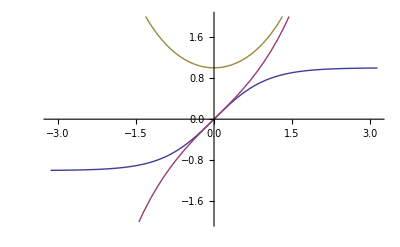

```mathematica
Plot[{Tanh[α],Sinh[α],Cosh[α]},{α,-π,π},PlotRange->2]
```

```mathematica
S=Λ.X
```

{c t Cosh[θ]-x Sinh[θ],x Cosh[θ]-c t Sinh[θ],y,z}

```mathematica
(* Velocity Addition *)
UX=X/(X[[1]]/c)//Simplify
US=S/(S[[1]]/c)//Simplify
```

{c,x/t,y/t,z/t}

{c,(c (x Cosh[θ]-c t Sinh[θ]))/(c t Cosh[θ]-x Sinh[θ]),(c y)/(c t Cosh[θ]-x Sinh[θ]),(c z)/(c t Cosh[θ]-x Sinh[θ])}

```mathematica
(*
x/t = ux = c Tanh[α],
y/t = uy = c Tanh[β],
z/t = uz = c Tanh[δ] *)
```

```mathematica
US/.{x-> c t Tanh[α],y->c t Tanh[β],z->c t Tanh[δ]}//Simplify
```

{c,c Tanh[α-θ],c Cosh[α] Sech[α-θ] Tanh[β],c Cosh[α] Sech[α-θ] Tanh[δ]}

```mathematica
Manipulate[
Plot[ {Tanh[α-θ],Tanh[-θ]},{θ,-π,π},PlotRange->1],
{α,-π,π}]
```

```mathematica
Manipulate[
Plot[ {Cosh[α] Sech[α-θ] Tanh[β],Tanh[-θ]},{θ,-π,π},PlotRange->1],
{α,-π,π},{β,-π,π}]
```